# Funciones

## Operadores

### Coin

```mathematica
-Graphics-;
```

```mathematica
n[α_,ϕ_]:={Sin[α]Cos[ϕ],Sin[α]Sin[ϕ],Cos[α]}
```

```mathematica
Paulis=PauliMatrix/@Range[3];
```

```mathematica
expCoin[θ_,α_,ϕ_]:=MatrixExp[(-ⅈ θ)/2.(n[α,ϕ].Paulis)]
```

```mathematica
Coin[θ_,α_,ϕ_,t_Integer]:=KroneckerProduct[SparseArray[Table[{i,i}->1.,{i,2 t+1}]],SparseArray[expCoin[θ,α,ϕ]]]
```

```mathematica
α=2 π/5;
ϕ=π;
t=1;
Coin[θ,α,ϕ,t]
```

SparseArray[…]

### Shift

```mathematica
Shift[t_Integer]:=SparseArray[Join[Table[{i,i+2},{i,Range[2,#-2,2]}],Table[{i,i-2},{i,Range[3,#,2]}]]->1.,{#,#}]&[2*(2*t+1)]
```

```mathematica
t=1;
Shift[t].{0,0,1,0,0,0}
```

{0.,0.,0.,0.,1.,0.}

### Unitaria

```mathematica
Unitary[θ_,α_,ϕ_,t_Integer]:=Shift[t].Coin[θ,α,ϕ,t]
```

```mathematica
α=2 π/5;
ϕ=π;
t=1;
Unitary[θ,α,ϕ,t]
```

SparseArray[…]

```mathematica
Unitary[paramsCoin_List,t_Integer]:=Module[{coinProduct},
coinProduct=Dot@@(Coin[##,t]&@@@Reverse[paramsCoin]);
Shift[t].coinProduct]
```

## Funciones cálculos

### Estados de la moneda

```mathematica
state0={1.,0.};
state1={0.,1.};
plusX=1/Sqrt[2]{1.,1.};
minusX=1/Sqrt[2]{1.,-1.};
plusY=1/Sqrt[2.]{1,ⅈ};
minusY=1/Sqrt[2.]{1,-ⅈ};
```

```mathematica
HVecs=N[Normalize/@Eigenvectors[HadamardMatrix[2]]];
HMinus=HVecs[[1]];
HPlus=HVecs[[2]];
```

### Estado aleatorio

```mathematica
QubitState[θ_,ϕ_]:={Cos[θ/2] ,Exp[I ϕ] Sin[θ/2] }
```

```mathematica
ClearAll@RandomQubitState
```

```mathematica
RandomQubitState[seed_:Automatic,fixedθ_:Automatic,fixedϕ_:Automatic]:=Module[{θ,ϕ,u1,u2},If[seed=!=Automatic,SeedRandom[seed]];
u1=RandomReal[];u2=RandomReal[];θ=If[fixedθ===Automatic,ArcCos[2 u1-1],fixedθ];
ϕ=If[fixedϕ===Automatic,2 Pi u2,fixedϕ];
{θ,ϕ,Cos[θ/2],Exp[I ϕ] Sin[θ/2]}]
```

```mathematica
RandomQubitState[123]
```

{1.65947,6.14386,0.67507,0.730605-0.102455 ⅈ}

```mathematica
RandomQubitState[123,π/2.,Automatic]
```

{1.5708,6.14386,0.707107,0.700255-0.0981984 ⅈ}

```mathematica
RandomQubitState[123,Automatic,Automatic]
```

{1.65947,6.14386,0.67507,0.730605-0.102455 ⅈ}

```mathematica
QubitState[1.6594742299456648,6.1438614455765235]
```

{0.67507,0.730605-0.102455 ⅈ}

### Hallar antípoda

```mathematica
FindAntipode[polar_,azimutal_]:=Module[{newPolar,newAzimutal},
{newPolar=π-polar,
newAzimutal=azimutal+π}
]
```

### Estado final de la caminata después de t pasos

```mathematica
DQWL[coin0_,θ_,α_,ϕ_,t_Integer]:=
Module[{psi},
psi=coin0;
Do[psi=Chop[#.ArrayPad[psi,2]]&[Unitary[θ,α,ϕ,i]],{i,t}];
psi
]
```

```mathematica
DQWL[coin0_,paramsCoin_List,t_Integer]:=
Module[{psi},
psi=coin0;
Do[psi=Chop[#.ArrayPad[psi,2]]&[Unitary[paramsCoin,i]],{i,t}];
psi
]
```

### Distribución de probabilidad

```mathematica
PosProbDistrib[psi_,tmax_]:=Chop[Total[Abs[psi[[#;;#+1]]]^2]&/@Range[1,2(2tmax+1),2]]
```

### Distribución de probabilidad para cada uno de los pasos

```mathematica
PosProbDisTime[coin0_,θ_,α_,ϕ_,t_Integer]:=Module[{psi,probs,p},
psi=coin0;
p=Table[
probs=PosProbDistrib[psi,i-1];
psi=Chop[#.ArrayPad[psi,2]]&[Unitary[N@θ,N@α,N@ϕ,i]];
ArrayPad[probs,t-(i-1)],{i,t+1}];
p
]
```

```mathematica
PosProbDisTime[coin0_,paramsCoin_List,t_Integer]:=Module[{psi,probs,p},
psi=coin0;
p=Table[
probs=PosProbDistrib[psi,i-1];
psi=Chop[#.ArrayPad[psi,2]]&[Unitary[N@paramsCoin,i]];
ArrayPad[probs,t-(i-1)],{i,t+1}];
p
]
```

### Valor de expectación

```mathematica
ExpecValue[posProbDisTime_List, t_Integer]:=Flatten[Chop[posProbDisTime.Range[-t,t]]]
```

### Determinar si la estrategia es ganadora o perdedora

```mathematica
WinningQ[expValsList_List] := 
  Which[
SameQ@@expValsList,"Indefinido",
    OrderedQ[expValsList], "Ganadora",
    OrderedQ[expValsList, GreaterEqual], "Perdedora",
    True, "No se puede determinar"
  ]
```

### Calcular posProbDistTime, expval y typeStrategy

```mathematica
CalculateData[coin0_,θ_,α_,ϕ_,t_Integer]:=Module[{posProbDistTime,expval,typeStrategy},
{posProbDistTime=PosProbDisTime[coin0,θ,α,ϕ,t],
expval=ExpecValue[posProbDistTime,t],
typeStrategy=WinningQ[expval]}
]
```

```mathematica
CalculateData[coin0_,paramsCoin_,t_Integer]:=Module[{posProbDistTime,expval,typeStrategy},
{posProbDistTime=PosProbDisTime[coin0,paramsCoin,t],
expval=ExpecValue[posProbDistTime,t],
typeStrategy=WinningQ[expval]}
]
```

### Fijar θ y α, variar ϕ

```mathematica
VaryingPhi[coin0_,θ_,α_,nϕ_Integer,t_Integer]:=Module[{ϕ},
Table[
Flatten[{ϕ=i *2π/nϕ,
CalculateData[coin0,θ,α,ϕ,t]},
1],
{i,0,nϕ-1}
]
]
```

### Fijar θ , variar α y ϕ

```mathematica
VaryingAlpha[coin0_,θ_,nα_Integer,nϕ_Integer,t_Integer]:=Module[{α},
Flatten[
Table[α=j*Pi/(nα-1);
Map[Prepend[#,α]&,
VaryingPhi[coin0,θ,α,nϕ,t]
],
{j,0,nα-1}],
1]
]
```

### Variar θ, α y ϕ

```mathematica
VaryingTheta[psi0_,nθ_Integer,nα_Integer,nϕ_Integer,t_Integer]:=Module[{θ},
Flatten[Table[θ=k*2*Pi/nθ;
Map[Prepend[#,θ]&,
VaryingAlpha[psi0,θ,nα,nϕ,t]
],
{k,0,nθ-1}],
1]
]
```

### Extraer datos para FixedTimeExpValPlot

```mathematica
ExtractDataExpVal[varyingAlpha_List,t_Integer]:=Flatten[{#[[1;;2]],#[[4,t+1]]}]&/@varyingAlpha
```

### Extraer datos para SphereGraph

```mathematica
ExtractDataSphereGraph[varyingAlpha_List]:=Flatten[{#[[1;;2]],#[[5]]}]&/@varyingAlpha
```

## Funciones gráficas

### Colores

```mathematica
Midnight=RGBColor["#311441"];
Sky=RGBColor["#35A3FA"];
AcuaGreen=RGBColor["#47F884"];
DirtyYellow=RGBColor["#E1DC46"];
HotOrange=RGBColor["#F4651D"];
Wine=RGBColor["#7D0402"];
ArticleColors=(Blend[{Midnight,Sky,AcuaGreen,DirtyYellow,HotOrange,Wine},#]&);
```

```mathematica
SphereColor=RGBColor["#DFF7FF"];
```

### Label coin

```mathematica
LabelCoinState[state0]:="0";
LabelCoinState[state1]:="1";
LabelCoinState[plusX]:="+_x"
LabelCoinState[minusX]:="-_x"
LabelCoinState[plusY]:="-_y"
LabelCoinState[minusY]:="-_y"
LabelCoinState[HMinus]:="H_-"
LabelCoinState[HPlus]:="H_+"
```

### Probabilidad respecto al tiempo

```mathematica
PosProbDisTimePlot[posProbDisTime_List,opts:OptionsPattern[ArrayPlot]]:=
ArrayPlot[posProbDisTime,
BaseStyle->{FontFamily->"Latin Modern Roman"},
LabelStyle->{FontFamily->"Latin Modern Roman"},
DataReversed->True,
ColorFunction->ArticleColors,
AspectRatio->1,
FrameLabel->(Style[#,FontSize->13]&/@{"",""}),
FrameTicks->{{Table[{i,i-1,0},{i,1,(2t+1-1)/2+1,(2t+1-1)/12}],None},{Table[{i,i-1-t,0},{i,1,2t+1,t}],None}},
FrameTicksStyle->13,
PlotRangePadding->0,
PlotLegends->BarLegend[
Automatic,
LegendLabel->""
],
opts
]
```

```mathematica
PosProbDisTimePlot[P2]
```

PosProbDisTimePlot[P2]

### Valor de expectación respecto al tiempo

```mathematica
Clear@ExpValVsTimePlot
```

```mathematica
ExpValVsTimePlot[expecValue_List,t_,opts:OptionsPattern[ListLinePlot]]:=
ListLinePlot[{Range[0,t],expecValue}ᵀ,
BaseStyle->{FontFamily->"Latin Modern Roman"},
LabelStyle->{FontFamily->"Latin Modern Roman"},
PlotRange->All,
Frame->True,
AspectRatio->1,
FrameLabel->(Style[#,FontSize->13]&/@{"",""}),
FrameTicksStyle->13,
Mesh->All,
PlotStyle->Thickness[0.005],
GridLines->{Range[Automatic,Automatic,50],Range[Automatic,Automatic,20]},
GridLinesStyle->Thin,
Evaluate@opts
]
```

```mathematica
ExpValVsTimePlot[{expecValues__List},t_,opts:OptionsPattern[ListLinePlot]]:=
ListLinePlot[{Range[0,t],#}ᵀ&/@{expecValues},
BaseStyle->{FontFamily->"Latin Modern Roman"},
LabelStyle->{FontFamily->"Latin Modern Roman"},
PlotRange->All,
Frame->True,
AspectRatio->1,
FrameLabel->(Style[#,FontSize->13]&/@{"",""}),
FrameTicksStyle->13,
PlotStyle->Thickness[0.005],
Mesh->All,
Evaluate@opts
]
```

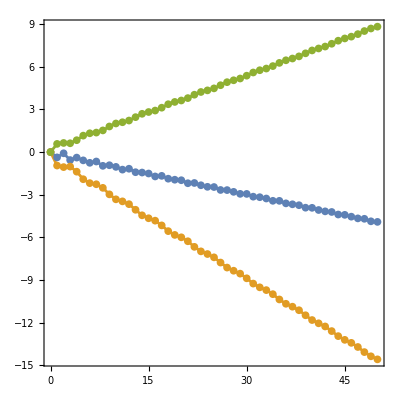

```mathematica
coin0=plusX;

θ1=π;
α1=0.39π;
ϕ1=1.3π;

θ2=3π/2;
α2=0.39π;
ϕ2=1.3π;

t=50;

G=CalculateData[coin0,θ1,α1,ϕ1,t];
H=CalculateData[coin0,θ2,α2,ϕ2,t];
J=CalculateData[coin0,{{θ1,α1,ϕ1},{θ2,α2,ϕ2}},t];

ExpValVsTimePlot[{G[[2]],H[[2]],J[[2]]},t,PlotLegends->{"","",""}]
```

```mathematica
ExpValVsTimeManipulate[coin0_,tmax_Integer]:=Manipulate[Module[{posProb,expecVal},
posProb=PosProbDisTime[coin0,θ,α,ϕ,t];
expecVal=ExpecValue[posProb,t];
ExpValVsTimePlot[expecVal,t]
],
{θ,0,2 Pi,Appearance->"Labeled"},
{α,0,Pi,Appearance->"Labeled"},
{ϕ,0,2 Pi,Appearance->"Labeled"}
]
```

### Valor de expectación para un tiempo fijo

```mathematica
ClearAll@FixedTimeExpValPlot
```

```mathematica
FixedTimeExpValPlot[data_List,fixedt_Integer,initCoinState_,θ_,nα_Integer,nϕ_Integer,opts:OptionsPattern[ListDensityPlot]]:=Module[{alphaTicks,phiTicks,alphaVals,phiVals,alphaLines,phiLines},
(*Extraer valores únicos y ordenarlos*)
alphaVals=Sort@DeleteDuplicates[data[[All,1]]];
phiVals=Sort@DeleteDuplicates[data[[All,2]]];

(*Calcular líneas intermedias entre valores:fronteras de celdas*)
alphaLines=MovingAverage[alphaVals,2]//Flatten;
phiLines=MovingAverage[phiVals,2]//Flatten;

(*Ticks en múltiplos de π/10 y π/5*)
alphaTicks=Table[{2*i π/nα,ToString[TraditionalForm[2*i π/nα]]},{i,0,nα}];
phiTicks=Table[{2*i*2π/nϕ,ToString[TraditionalForm[2*i*2π/nϕ]]},{i,0,nϕ}];

ListDensityPlot[data,
FrameLabel->{"α","ϕ"},
FrameTicks->{{phiTicks,None},{alphaTicks,None}},
ColorFunction->(ColorData["Rainbow"][Rescale[#,{-10,10}]]&),
ColorFunctionScaling->False,
PlotRange->All,
PlotLegends->BarLegend[{ColorData[{"Rainbow",{-10,10}}][#]&,{-10,10}}],
InterpolationOrder->0,
ImageSize->200,
Epilog->{Table[{Black,Thin,Line[{{x,Min[phiVals]},{x,Max[phiVals]}}]},{x,alphaLines}],(*Líneas verticales*)
Table[{Black,Thin,Line[{{Min[alphaVals],y},{Max[alphaVals],y}}]},{y,phiLines}](*Líneas horizontales*)
}//Flatten,
PlotLabel->Row[{"c_0 = ",LabelCoinState[initCoinState],"     θ = ",θ,",     = ",fixedt}],
opts
]
]
```

```mathematica
FixedTimeExpValPlot[data_List,fixedt_Integer,initCoinState_,θ_,nα_Integer,nϕ_Integer,αLabels_Integer,ϕLabels_Integer,opts:OptionsPattern[ListDensityPlot]]:=Module[{alphaTicks,phiTicks,alphaVals,phiVals,alphaLines,phiLines},
(*Extraer valores únicos y ordenarlos*)
alphaVals=Sort@DeleteDuplicates[data[[All,1]]];
phiVals=Sort@DeleteDuplicates[data[[All,2]]];

(*Calcular líneas intermedias entre valores:fronteras de celdas*)
alphaLines=MovingAverage[alphaVals,2]//Flatten;
phiLines=MovingAverage[phiVals,2]//Flatten;

(*Ticks en múltiplos de π/10 y π/5*)
alphaTicks=Table[{αLabels*i π/nα,ToString[TraditionalForm[αLabels*i π/nα]]},{i,0,nα}];
phiTicks=Table[{ϕLabels*i*2π/nϕ,ToString[TraditionalForm[ϕLabels*i*2π/nϕ]]},{i,0,nϕ}];

ListDensityPlot[data,
FrameLabel->{"α","ϕ"},
FrameTicks->{{phiTicks,None},{alphaTicks,None}},
ColorFunction->(ColorData["Rainbow"][Rescale[#,{-10,10}]]&),
ColorFunctionScaling->False,
PlotRange->All,
PlotLegends->BarLegend[{ColorData[{"Rainbow",{-10,10}}][#]&,{-10,10}}],
InterpolationOrder->0,
ImageSize->200,
Epilog->{Table[{Black,Thin,Line[{{x,Min[phiVals]},{x,Max[phiVals]}}]},{x,alphaLines}],(*Líneas verticales*)
Table[{Black,Thin,Line[{{Min[alphaVals],y},{Max[alphaVals],y}}]},{y,phiLines}](*Líneas horizontales*)
}//Flatten,
PlotLabel->Row[{"c_0 = ",LabelCoinState[initCoinState],"     θ = ",θ,",     = ",fixedt}],
opts
]
]
```

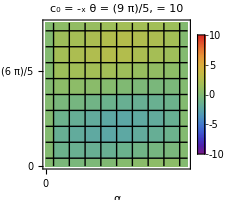

```mathematica
coin0=minusX;
θ=9π/5;
nα=10;
nϕ=10;
t=10;
fixedt=10;
res=VaryingAlpha[coin0,θ,nα,nϕ,t];
data=ExtractDataExpVal[res,fixedt];
FixedTimeExpValPlot[data,fixedt,coin0,θ,nα,nϕ]
```

### Marcar el punto en la esfera de Bloch

```mathematica
PolarPoint[{r_,polar_,azimutal_}]:=Point[r*{Sin[polar] Cos[azimutal],Sin[polar] Sin[azimutal],Cos[polar]}]
```

```mathematica
ClearAll@SphereGraph
```

```mathematica
SphereGraph[data_List,initCoinState_,θ_,opts:OptionsPattern[Graphics3D]]:=Module[{sphere},
sphere=Graphics3D[{
Opacity[0.95],Glow[SphereColor],Black,Sphere[],
Opacity[1],PointSize[0.03],

Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{1.2,0,0}}],
Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{0,1.2,0}}],
Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{0,0,1.2}}],

Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{-1.2,0,0}}],
Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{0,-1.2,0}}],
Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{0,0,-1.2}}],

Text[Style["",14,Black],{1.3,0,0}],
Text[Style["",14,Black],{0,1.3,0}],
Text[Style["",14,Black],{0,0,1.3}],

RGBColor["#00D52C"],Table[PolarPoint[{1,p[[1]],p[[2]]}],{p,Select[data,#[[3]]=="Ganadora"&]}],
Red,Table[PolarPoint[{1,p[[1]],p[[2]]}],{p,Select[data,#[[3]]=="Perdedora"&]}],
Black,Table[PolarPoint[{1,p[[1]],p[[2]]}],{p,Select[data,#[[3]]=="Indefinido"&]}],
Gray,Table[PolarPoint[{1,p[[1]],p[[2]]}],{p,Select[data,#[[3]]=="No se puede determinar"&]}]
},
Boxed->False,
PlotLabel->Row[{"c_0 = ",LabelCoinState[initCoinState],",    θ = ",θ}],
opts
]
]
```

```mathematica
coin0=minusX;
θ=9π/5;
nα=10;
nϕ=10;
t=10;
res=VaryingAlpha[coin0,θ,nα,nϕ,t];
data=ExtractDataSphereGraph[res];
SphereGraph[data,coin0,θ]
```

-Graphics3D-

### Valor de expectación contra θ

```mathematica
ExpValVsThetaPlot[coin0_,α_,ϕ_,tmax_Integer,opts:OptionsPattern[ListLinePlot]]:=Module[{thetaVals,expecVals},
thetaVals=Subdivide[0,2 π,100];

expecVals=Table[Table[ExpecValue[PosProbDisTime[coin0,θ,α,ϕ,t],t][[t+1]],{θ,thetaVals}],{t,1,tmax}];

ListLinePlot[Transpose[{thetaVals,#}]&/@expecVals,
PlotLegends->Placed[LineLegend[Range[1,tmax],
LabelStyle->{FontSize->12},
LegendLabel->Style["",FontSize->13]],
Right
],
Frame->True,
FrameLabel->{"",""},
FrameTicks->{{Automatic,Automatic},{Table[{k π/4,ToString[TraditionalForm[k π/4]]},{k,0,8}],Automatic}},
PlotRange->{All,{-(t+0.05t),tmax+0.05tmax}},
PlotStyle->ColorData[97]/@Range[tmax],
ImageSize->350,
opts]
]
```

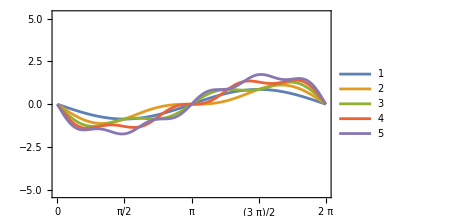

```mathematica
coin0=plusX;
α=π/2.;
ϕ=π/3.;
t=5;

ExpValVsThetaPlot[coin0,α,ϕ,t]
```

```mathematica
ClearAll@ExpValVsThetaManipulate
```

```mathematica
ExpValVsThetaManipulate[coin0_,tmax_Integer:5]:=Manipulate[
ExpValVsThetaPlot[coin0,α,ϕ,tmax],
{α,0,π,Appearance->"Labeled"},
{ϕ,0,2 π,Appearance->"Labeled"}
]
```

# Prueba

```mathematica
{α,ϕ}={4Pi/5.,11Pi/9.};
{β,γ}={Pi/2.,Pi/8.};
```

```mathematica
a=Cos[β/2];
b=Exp[ⅈ γ]Sin[β/2];
```

```mathematica
θ1=ArcCos[(Cos[2(γ-ϕ)]-Sin[α]^2 Cos[γ-ϕ]^2)/(1-Sin[α]^2 Cos[γ-ϕ]^2)]
```

0.743245

```mathematica
θ2=2π-ArcCos[(Cos[2(γ-ϕ)]-Sin[α]^2 Cos[γ-ϕ]^2)/(1-Sin[α]^2 Cos[γ-ϕ]^2)]
```

5.53994

```mathematica
δ=γ-ϕ
```

-3.44703

```mathematica
u[θ_,α_]:=Cos[θ/2]+ⅈ Cos[α]Sin[θ/2]
```

```mathematica
u[θ2,α]
```

-0.931739-0.293776 ⅈ

```mathematica
uAnl[θ_,δ_,α_]:=(-Abs[Cos[δ] Cos[α]]+ⅈ Cos[α]Abs[Sin[δ]])/Sqrt[1-Sin[α]^2 Cos[δ]^2]
```

```mathematica
uAnl[θ2,δ,α]
```

-0.931739-0.293776 ⅈ

```mathematica
v[θ_,ϕ_,α_]:=-ⅈ Exp[ⅈ ϕ]Sin[α]Sin[θ/2]
```

```mathematica
v[θ2,ϕ,α]
```

-0.137197+0.163505 ⅈ

```mathematica
vAnl[θ_,ϕ_,δ_,α_]:=-ⅈ Exp[ⅈ ϕ] (Sin[α] Abs[Sin[δ]])/Sqrt[1-Sin[α]^2 Cos[δ]^2]
```

```mathematica
vAnl[θ2,ϕ,δ,α]
```

-0.137197+0.163505 ⅈ

```mathematica
expCoin[θ2,α,ϕ]//MatrixForm
```

(-0.931739+0.293776 ⅈ | 0.137197+0.163505 ⅈ
-0.137197+0.163505 ⅈ | -0.931739-0.293776 ⅈ)

```mathematica
{{Conjugate[u[θ2,α]],-Conjugate[v[θ2,ϕ,α]]},{v[θ2,ϕ,α],u[θ2,α]}}//MatrixForm
```

(-0.931739+0.293776 ⅈ | 0.137197+0.163505 ⅈ
-0.137197+0.163505 ⅈ | -0.931739-0.293776 ⅈ)

```mathematica
Pplus1=a Conjugate[u[θ2,α]]-b Conjugate[v[θ2,ϕ,α]]
```

-0.613455+0.351672 ⅈ

```mathematica
Pminus1=a v[θ2,ϕ,α]-b u[θ2,α]
```

0.43218+0.559661 ⅈ

```mathematica
Abs[Pplus1]^2-Abs[Pminus1]^2//Chop
```

0

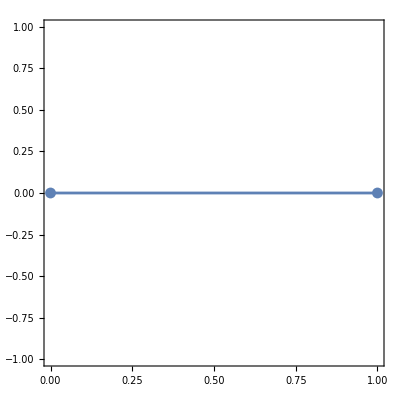

```mathematica
t=1;
coin0=QubitState[β,γ];
θ=θ2;
ExpValVsTimePlot[CalculateData[coin0,θ,α,ϕ,t][[2]],t]
```

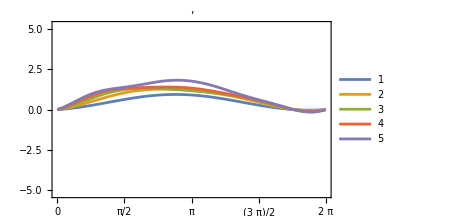

```mathematica
coin0=QubitState[β,γ];
t=5;
ExpValVsThetaPlot[coin0,α,ϕ,t,
PlotLabel->Row[{",     "}]
]
```

# Prueba 2

## Funciones

```mathematica
Coeffs[β_,γ_]:=Module[{a,b},
a=Cos[β/2];
b=Exp[ⅈ γ]Sin[β/2];
{a,b}
]
```

```mathematica
Thetas[α_,ϕ_,β_,γ_]:=Module[{θ1,θ2},
θ1=ArcCos[(Cos[2(γ-ϕ)]-Sin[α]^2 Cos[γ-ϕ]^2)/(1-Sin[α]^2 Cos[γ-ϕ]^2)];
θ2=2π-ArcCos[(Cos[2(γ-ϕ)]-Sin[α]^2 Cos[γ-ϕ]^2)/(1-Sin[α]^2 Cos[γ-ϕ]^2)];
{θ1,θ2}
]
```

```mathematica
u[θ_,α_]:=Cos[θ/2]+ⅈ Cos[α]Sin[θ/2]
```

```mathematica
uAnl[s_,α_,ϕ_,γ_]:=(s Abs[Cos[γ-ϕ] Cos[α]]+ⅈ Cos[α]Abs[Sin[γ-ϕ]])/Sqrt[1-Sin[α]^2 Cos[γ-ϕ]^2]
```

```mathematica
v[θ_,α_,ϕ_]:=-ⅈ Exp[ⅈ ϕ]Sin[α]Sin[θ/2]
```

```mathematica
vAnl[α_,ϕ_,γ_]:=-ⅈ Exp[ⅈ ϕ] (Sin[α] Abs[Sin[γ-ϕ]])/Sqrt[1-Sin[α]^2 Cos[γ-ϕ]^2]
```

```mathematica
ExpValExp[θ_,α_,ϕ_,β_,γ_]:=Module[{a,b,AmpPplus1,AmpPminus1},
a=Cos[β/2];
b=Exp[ⅈ γ]Sin[β/2];
AmpPplus1=a Conjugate[u[θ,α]]-b Conjugate[v[θ,ϕ,α]];
AmpPminus1=a v[θ,ϕ,α]-b u[θ,α];
Abs[AmpPplus1]^2-Abs[AmpPminus1]^2//Chop
]
```

```mathematica
ExpValAnl[s_,α_,ϕ_,β_,γ_]:=Module[{a,b,AmpPplus1,AmpPminus1},
a=Cos[β/2];
b=Exp[ⅈ γ]Sin[β/2];
AmpPplus1=a Conjugate[uAnl[s,α,ϕ,γ]]-b Conjugate[vAnl[α,ϕ,γ]];
AmpPminus1=a vAnl[α,ϕ,γ]-b uAnl[s,α,ϕ,γ];
Abs[AmpPplus1]^2-Abs[AmpPminus1]^2//Chop
]
```

## Valores

```mathematica
a=Cos[β/2];
b=Exp[ⅈ γ]Sin[β/2];
```

```mathematica
AmpPplus11=a Conjugate[u[θ[[1]],α]]-b Conjugate[v[θ[[1]],ϕ,α]]
```

0.719132-0.0147928 ⅈ

```mathematica
AmpPminus11=a v[θ[[1]],ϕ,α]-b u[θ[[1]],α]
```

-0.700982+0.161228 ⅈ

```mathematica
Abs[AmpPplus11]^2-Abs[AmpPminus11]^2//Chop
```

0

```mathematica
AmpPplus12=a Conjugate[u[θ[[2]],α]]-b Conjugate[v[θ[[2]],ϕ,α]]
```

-0.688456-0.0147928 ⅈ

```mathematica
AmpPminus12=a v[θ[[2]],ϕ,α]-b u[θ[[2]],α]
```

0.66401-0.182429 ⅈ

```mathematica
Abs[AmpPplus12]^2-Abs[AmpPminus12]^2//Chop
```

0

```mathematica
SeedRandom[607];
{α,β}={RandomReal[{0,Pi}],Pi/2.}
{ϕ,γ}=RandomReal[{0,2Pi},2]
```

{1.36121,1.5708}

{6.05675,6.03655}

```mathematica
θ=Thetas[α,ϕ,β,γ]
```

{0.193677,6.08951}

```mathematica
ExpValExp[θ[[1]],α,ϕ,β,γ]
```

0

```mathematica
ExpValAnl[1,α,ϕ,β,γ]
```

0

```mathematica
ExpValExp[θ[[2]],α,ϕ,β,γ]
```

0

```mathematica
ExpValAnl[-1,α,ϕ,β,γ]
```

0

```mathematica
t=1;
coin0=QubitState[β,γ];
ExpValVsTimePlot[CalculateData[coin0,θ[[1]],α,ϕ,t][[2]],t]
```

-Graphics-

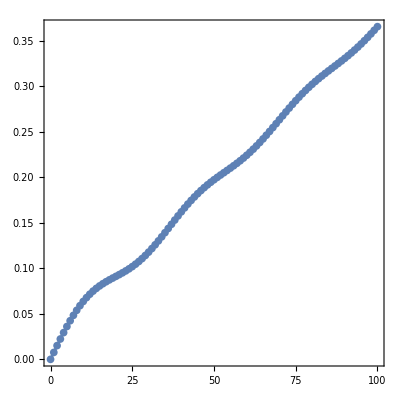

```mathematica
t=100;
coin0=QubitState[β,γ];
ExpValVsTimePlot[CalculateData[coin0,θ[[2]],α,ϕ,t][[2]],t]
```

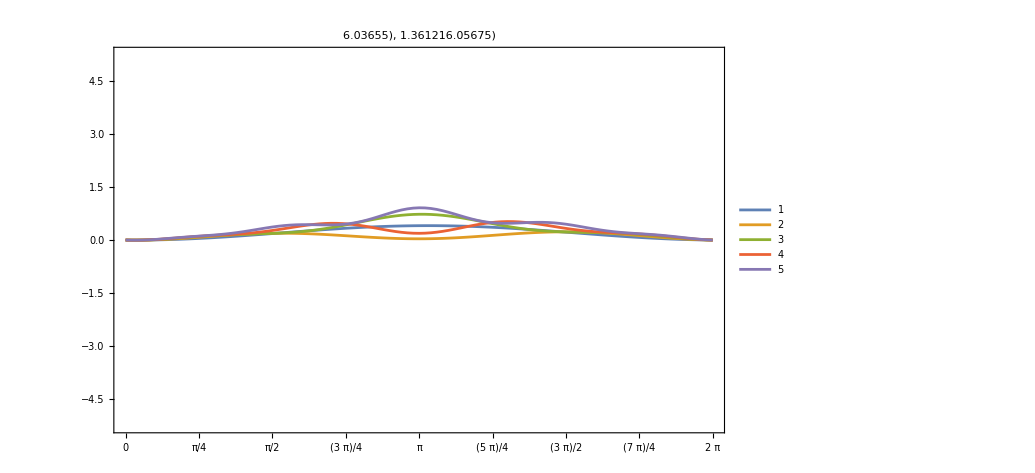

```mathematica
coin0=QubitState[β,γ];
t=5;
ExpValVsThetaPlot[coin0,α,ϕ,t,
PlotLabel->Row[{"",γ,"),     ",α,"",ϕ,")"}]
]
```

```mathematica
Table[{(i π)/8,(i π)/8//N},{i,0,16}]
```

{{0,0.},{π/8,0.392699},{π/4,0.785398},{(3 π)/8,1.1781},{π/2,1.5708},{(5 π)/8,1.9635},{(3 π)/4,2.35619},{(7 π)/8,2.74889},{π,3.14159},{(9 π)/8,3.53429},{(5 π)/4,3.92699},{(11 π)/8,4.31969},{(3 π)/2,4.71239},{(13 π)/8,5.10509},{(7 π)/4,5.49779},{(15 π)/8,5.89049},{2 π,6.28319}}

```mathematica
θ
```

{0.193677,6.08951}

```mathematica
coin0=QubitState[β,γ];
t=5;
ExpValVsThetaManipulate[coin0]
```

MatrixExp::matsq: Argument 0.+0. ⅈ at position 1 is not a non-empty square matrix.

SparseArray::list: List expected at position 1 in SparseArray[MatrixExp[0.+0. ⅈ]].

MatrixExp::matsq: Argument 0 at position 1 is not a non-empty square matrix.

SparseArray::list: List expected at position 1 in SparseArray[MatrixExp[0]].

Part::take: Cannot take positions 3 through 4 in ….

Part::take: Cannot take positions 5 through 6 in ….

MatrixExp::matsq: Argument 0.+0. ⅈ at position 1 is not a non-empty square matrix.

General::stop: Further output of MatrixExp::matsq will be suppressed during this calculation.

SparseArray::list: List expected at position 1 in SparseArray[MatrixExp[0.+0. ⅈ]].

General::stop: Further output of SparseArray::list will be suppressed during this calculation.

ArrayPad::arr: First argument … to ArrayPad should be an array.

Part::take: Cannot take positions 3 through 4 in ….

General::stop: Further output of Part::take will be suppressed during this calculation.

ArrayPad::arr: First argument … to ArrayPad should be an array.

General::stop: Further output of ArrayPad::arr will be suppressed during this calculation.

# Otros

```mathematica
rhof=DQWL[coin0,θ2,α,ϕ,1]
```

{0,-0.626206-0.32843 ⅈ,0,0,-0.613455+0.351672 ⅈ,0}

```mathematica
PosProbDistrib[rhof,1]
```

{0.5,0,0.5}

```mathematica
psi0=coin0;
psi1=Chop[#.ArrayPad[psi0,2]]&[Unitary[N@θ2,N@α,N@ϕ,1]]
```

{0,-0.626206-0.32843 ⅈ,0,0,-0.613455+0.351672 ⅈ,0}

```mathematica
probs1=PosProbDistrib[psi2,1]
```

Part::take: Cannot take positions 1 through 2 in psi2.

Part::take: Cannot take positions 3 through 4 in psi2.

Part::take: Cannot take positions 5 through 6 in psi2.

General::stop: Further output of Part::take will be suppressed during this calculation.

{Total[Abs[psi2⟦1;;2⟧]^2],Total[Abs[psi2⟦3;;4⟧]^2],Total[Abs[psi2⟦5;;6⟧]^2]}

```mathematica
P=PosProbDisTime[coin0,θ2,α,ϕ,1]
```

{{0,1.,0},{0.5,0,0.5}}

```mathematica
ExpecValue[P, 1]
```

{0,0}

```mathematica
CalculateData[coin0,θ2,α,ϕ,1][[2]]
```

{0,0}

```mathematica
expecVals=ExpecValue[PosProbDisTime[coin0,θ2,α,ϕ,1],1]
```

{0,0}

```mathematica
θ2
```

5.53994

```mathematica
(7π)/4.
```

5.49779

# Analytics

```mathematica
ClearAll@{s,a,b,α,ϕ,β,γ}
```

```mathematica
uAnl[s,α,ϕ,γ]
```

(s Abs[Cos[α] Cos[γ-ϕ]]+ⅈ Abs[Sin[γ-ϕ]] Cos[α])/(√(1-Cos[γ-ϕ]^2 Sin[α]^2))

```mathematica
uAnl[s,α,ϕ,γ]Conjugate[uAnl[s,α,ϕ,γ]]//FullSimplify
```

1/(√(1-Cos[γ-ϕ]^2 Sin[α]^2))Conjugate[1/(√(1-Cos[γ-ϕ]^2 Sin[α]^2))] (s Abs[Cos[α] Cos[γ-ϕ]]+ⅈ Abs[Sin[γ-ϕ]] Cos[α]) (Abs[Cos[α] Cos[γ-ϕ]] Conjugate[s]-ⅈ Abs[Sin[γ-ϕ]] Cos[Conjugate[α]])

```mathematica
2 Re[-Exp[ⅈ γ] uAnl[-1,α,ϕ,γ] Conjugate[vAnl[α,ϕ,γ]]]//FullSimplify
```

2 Re[1/(√(1-Cos[γ-ϕ]^2 Sin[α]^2))ⅇ^(ⅈ (γ-Conjugate[ϕ])) Abs[Sin[γ-ϕ]] Conjugate[Sin[α]/(√(1-Cos[γ-ϕ]^2 Sin[α]^2))] (ⅈ Abs[Cos[α] Cos[γ-ϕ]]+Abs[Sin[γ-ϕ]] Cos[α])]

```mathematica
ClearAll@{a,b,u,v}
```

```mathematica
a=1/Sqrt[2];
b=Exp[ⅈ γ]/Sqrt[2];
```

```mathematica
FullSimplify[(a Conjugate[u]-b Conjugate[v]) (a u-Conjugate[b] v)-(a v+b u) (a Conjugate[v]+Conjugate[b] Conjugate[u]),
Assumptions->Element[γ,Reals]]
```

-ⅇ^(-ⅈ γ) (v Conjugate[u]+ⅇ^(2 ⅈ γ) u Conjugate[v])

```mathematica
-ⅇ^(-ⅈ γ) (v Conjugate[u]+ⅇ^(2 ⅈ γ) u Conjugate[v])//Expand
```

-ⅇ^(-ⅈ γ) v Conjugate[u]-ⅇ^(ⅈ γ) u Conjugate[v]